```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}];
```

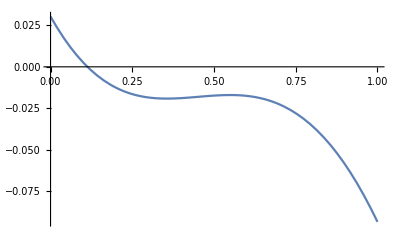

```mathematica
Plot[Ggauss[q, 3.316, 0.375]-q, {q, 0, 1}]
```

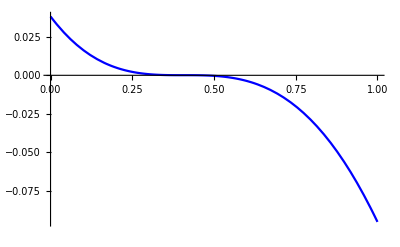

```mathematica
Plot[Ggauss[q,3.136,0.3543]-q,{q,0,1},PlotStyle->RGBColor[0.,0.,1.], PlotStyle->Dashed]
```

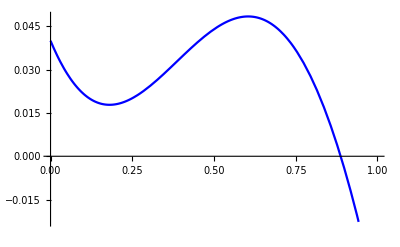

```mathematica
Plot[Ggauss[q,4,0.35]-q,{q,0,1},PlotStyle->RGBColor[0.,0.,1.], PlotStyle->Dashed]
```

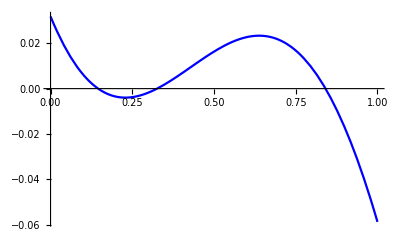

```mathematica
Plot[Ggauss[q,4,0.371]-q,{q,0,1},PlotStyle->RGBColor[0.,0.,1.], PlotStyle->Dashed]
```

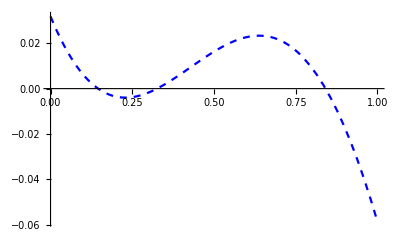

```mathematica
Plot[Ggauss[q,4,0.371]-q,{q,0,1},PlotStyle->Directive[RGBColor[0.,0.,1.],Dashed]]
```

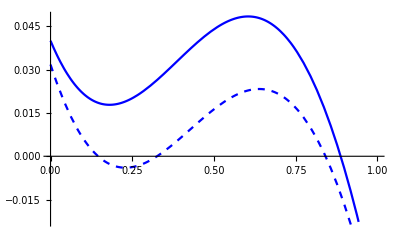

```mathematica
Show[%36, %38, PlotLegends->LineLegend[{0.35, 0.371}, LegendLabel->z]]
```

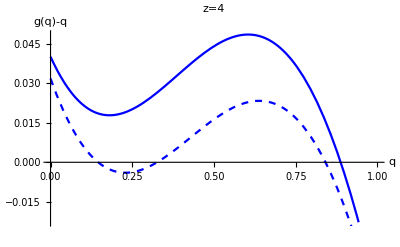

```mathematica
Show[%41,AxesLabel->{HoldForm[q],HoldForm[g[q]-q]},PlotLabel->HoldForm[z=4],LabelStyle->{GrayLevel[0]}, PlotLegends->Placed[LineLegend[{0.35, 0.371},LabelStyle->{GrayLevel[0.3],Bold,18},LegendLabel->z,LegendLayout->{"Row",2}],{0.75,0.25}]]
```

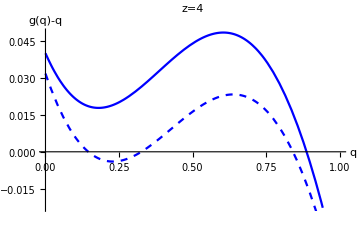

```mathematica
Show[%43,ImageSize->{360,232},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/single_layer_g-q.eps",%45,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/single_layer_g-q.eps